```mathematica
SetDirectory["~/mthesis/graphanalysis"]
data=Import["pkg-dep-growth"];
```

/home/remco/UT/Vakken/410004 Master Thesis Business Administration/graphanalysis

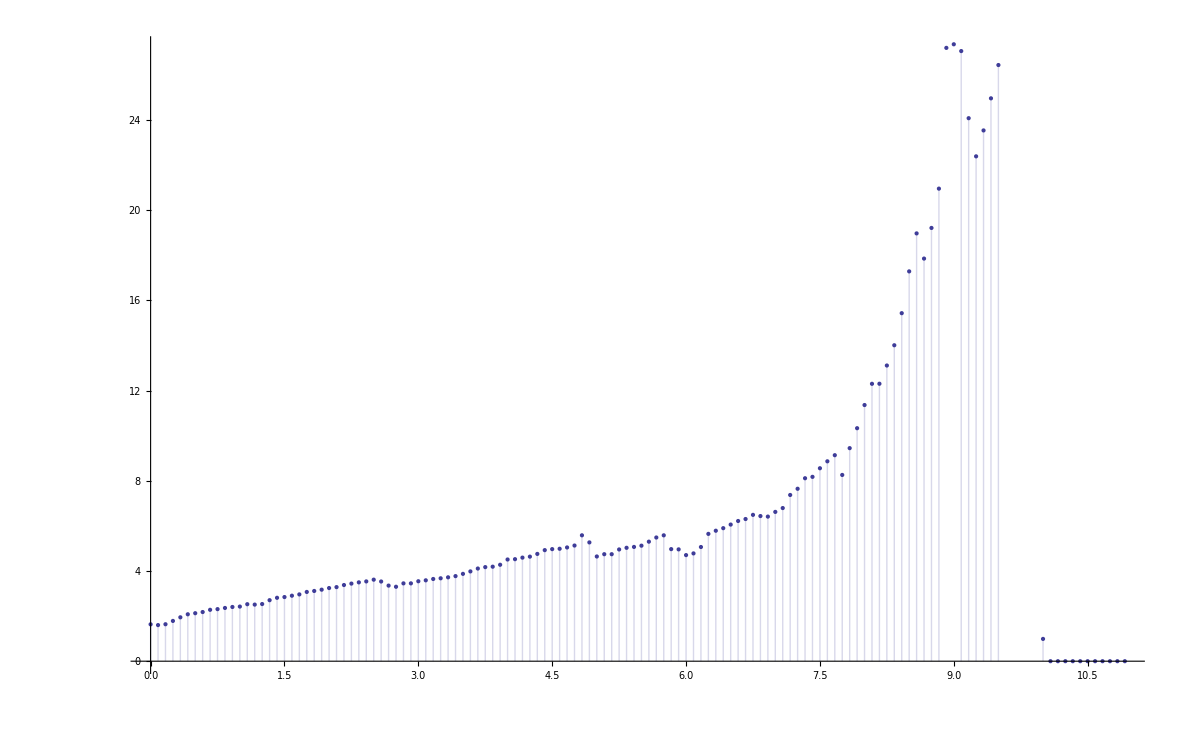

```mathematica
ListPlot[Inner[List,data⟦1;;-1,1⟧/12,data⟦1;;-1,2⟧,List],Filling->Bottom]
```

```mathematica
Export["depsAfterIntroduction.pdf",%,ImageResolution->300]
```

depsAfterIntroduction.pdf

```mathematica
ListPlot[Table[{t,NumDeps[t]},{t,1,130}]]
```

Part::partw: Part 133 of {{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {2, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {3, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {4, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {5, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {6, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {7, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {8, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {9, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, « 122 »} does not exist.

Part::partw: Part 134 of {{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {2, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {3, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {4, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {5, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {6, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {7, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {8, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, {9, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 256 »}, « 122 »} does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

$Aborted

```mathematica
DepTrace[n_]:=Inner[List,2000+data⟦1;;-4,1⟧/12-(n-1)/12,data⟦1;;-4,2n⟧/data⟦1;;-4,2n+1⟧,List];
```

```mathematica
DepTrace[1]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of indet will be suppressed during this calculation.

{{2000,Indeterminate},{24001/12,Indeterminate},{12001/6,Indeterminate},{8001/4,Indeterminate},{6001/3,Indeterminate},{24005/12,Indeterminate},{4001/2,Indeterminate},{24007/12,Indeterminate},{6002/3,Indeterminate},{8003/4,Indeterminate},{12005/6,Indeterminate},{24011/12,Indeterminate},{2001,Indeterminate},{24013/12,Indeterminate},{12007/6,Indeterminate},{8005/4,Indeterminate},{6004/3,Indeterminate},{24017/12,Indeterminate},{4003/2,Indeterminate},{24019/12,Indeterminate},{6005/3,Indeterminate},{8007/4,Indeterminate},{12011/6,Indeterminate},{24023/12,Indeterminate},{2002,Indeterminate},{24025/12,Indeterminate},{12013/6,Indeterminate},{8009/4,Indeterminate},{6007/3,Indeterminate},{24029/12,Indeterminate},{4005/2,Indeterminate},{24031/12,Indeterminate},{6008/3,Indeterminate},{8011/4,Indeterminate},{12017/6,Indeterminate},{24035/12,Indeterminate},{2003,Indeterminate},{24037/12,Indeterminate},{12019/6,Indeterminate},{8013/4,Indeterminate},{6010/3,Indeterminate},{24041/12,Indeterminate},{4007/2,Indeterminate},{24043/12,Indeterminate},{6011/3,Indeterminate},{8015/4,Indeterminate},{12023/6,Indeterminate},{24047/12,Indeterminate},{2004,Indeterminate},{24049/12,Indeterminate},{12025/6,Indeterminate},{8017/4,Indeterminate},{6013/3,Indeterminate},{24053/12,Indeterminate},{4009/2,Indeterminate},{24055/12,Indeterminate},{6014/3,Indeterminate},{8019/4,Indeterminate},{12029/6,Indeterminate},{24059/12,Indeterminate},{2005,Indeterminate},{24061/12,Indeterminate},{12031/6,Indeterminate},{8021/4,Indeterminate},{6016/3,Indeterminate},{24065/12,Indeterminate},{4011/2,Indeterminate},{24067/12,Indeterminate},{6017/3,Indeterminate},{8023/4,Indeterminate},{12035/6,Indeterminate},{24071/12,Indeterminate},{2006,Indeterminate},{24073/12,Indeterminate},{12037/6,Indeterminate},{8025/4,Indeterminate},{6019/3,Indeterminate},{24077/12,Indeterminate},{4013/2,Indeterminate},{24079/12,Indeterminate},{6020/3,Indeterminate},{8027/4,Indeterminate},{12041/6,Indeterminate},{24083/12,Indeterminate},{2007,Indeterminate},{24085/12,Indeterminate},{12043/6,Indeterminate},{8029/4,Indeterminate},{6022/3,Indeterminate},{24089/12,Indeterminate},{4015/2,Indeterminate},{24091/12,Indeterminate},{6023/3,Indeterminate},{8031/4,Indeterminate},{12047/6,Indeterminate},{24095/12,Indeterminate},{2008,Indeterminate},{24097/12,Indeterminate},{12049/6,Indeterminate},{8033/4,Indeterminate},{6025/3,Indeterminate},{24101/12,Indeterminate},{4017/2,Indeterminate},{24103/12,Indeterminate},{6026/3,Indeterminate},{8035/4,Indeterminate},{12053/6,Indeterminate},{24107/12,Indeterminate},{2009,Indeterminate},{24109/12,Indeterminate},{12055/6,Indeterminate},{8037/4,Indeterminate},{6028/3,Indeterminate},{24113/12,Indeterminate},{4019/2,Indeterminate},{24115/12,Indeterminate},{6029/3,Indeterminate},{8039/4,Indeterminate},{12059/6,Indeterminate},{24119/12,Indeterminate},{2010,Indeterminate},{24121/12,Indeterminate},{12061/6,Indeterminate},{8041/4,Indeterminate},{6031/3,Indeterminate},{24125/12,Indeterminate},{4021/2,Indeterminate},{24127/12,Indeterminate},{6032/3,Indeterminate}}

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of indet will be suppressed during this calculation.

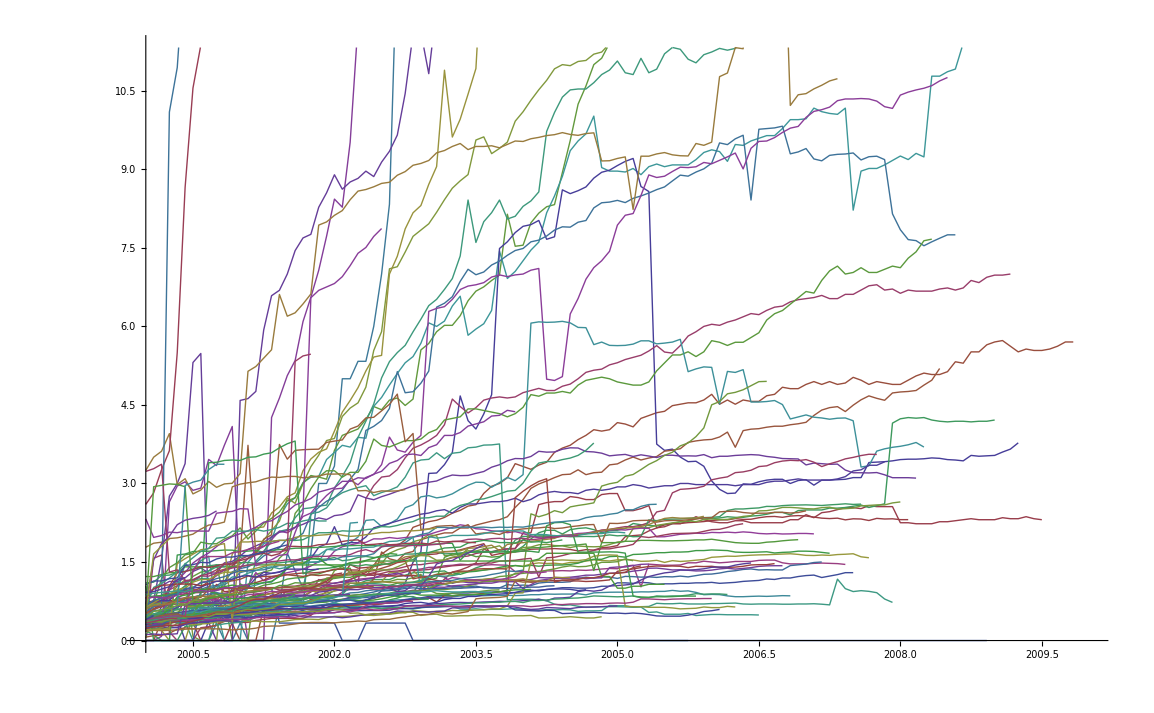

```mathematica
ListLinePlot[Table[DepTrace[n],{n,1,128}]]
```